```mathematica
priorcov = Import["/Users/sperkins/git-repos/gw_analysis_tools/tests/data/multi_gaussian_prior_cov.csv"]
likecov = Import["/Users/sperkins/git-repos/gw_analysis_tools/tests/data/multi_gaussian_like_cov.csv"]
priormean = Import["/Users/sperkins/git-repos/gw_analysis_tools/tests/data/multi_gaussian_prior_mean.csv"]
likemean = Import["/Users/sperkins/git-repos/gw_analysis_tools/tests/data/multi_gaussian_like_mean.csv"]
```

{{1}}

{{1}}

{{10}}

{{0}}

```mathematica
post[x_]:= (ⅇ^(-1/2 (x - likemean[[1]])^2/(likecov[[1]][[1]])))/(√(2π likecov[[1]][[1]]))(ⅇ^(-1/2 (x - priormean[[1]])^2/(priorcov[[1]][[1]])))/(√(2π priorcov[[1]][[1]]))
```

```mathematica
post[y]
```

{(ⅇ^(-1/2 (-10+y)^2-y^2/2))/(2 π)}

```mathematica
norm = Integrate[post[x],{x,-∞,∞}]
```

{1/(2 ⅇ^25 √π)}

```mathematica
mean =Integrate[x post[x]/norm,{x,-∞,∞}]
```

{5}

```mathematica
var =√Integrate[(x-mean)^2 post[x]/norm,{x,-∞,∞}]//Simplify
```

{1/(√2)}

```mathematica
√(Integrate[x^2 post[x]/norm,{x,-∞,∞}] - (Integrate[x post[x]/norm,{x,-∞,∞}])^2)
```

{1/(√2)}

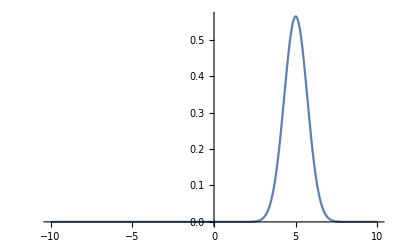

```mathematica
Plot[post[x]/norm,{x,-10,10},PlotRange->Full]
```